```mathematica
<<MaTeX`
```

### 2D Zernike moments

```mathematica
(* plotting staff, auxilary functions *)
(* convert expression (fucntion) from polar coordinates to cartesian *)
r2c[e_]:=Simplify[TrigExpand[e]/.{Sin[θ]:>y/r,Cos[θ]:>x/r}/.r^n_:>(x^2+y^2)^(n/2)] 
(*r2c3d[e_]:=Simplify[TrigExpand[e]/.{Sin[θ]:>y/r,Cos[θ]:>z/r, }/.r^n_:>(x^2+y^2+ z^2)^(n/2)] *)
(*  *)
zPlot[e_]:=With[{f= r2c[e]},DensityPlot[  f,{x,-1,1},{y,-1,1},RegionFunction:>(#1^2+#2^2≤1&), PlotPoints->12,Frame->False, ImageSize->120, ColorFunction->"BlueGreenYellow"]]
```

```mathematica
{maxX, maxY, maxZ} = {65,65, 65};
{dx, dy, dz} = {2/(maxX-1), 2/(maxY-1), 2/(maxZ-1)};

(* radial polynomials *)
(* n ≥ m , n - m is even *)
R[n_, m_, r_]:=Sum[((-1)^k(n-k)!)/(k! ((n+m)/2 - k)! ((n-m)/2 - k)!)r^(n - 2 k),{k,0, (n - m)/2,1}]

(* Zernike polynomials *)
Z[n_, m_,r_, θ_]:=ZernikeR[Abs@n,Abs@m,r]*If[m ≥0, Cos[m θ], Sin[Abs@m θ]] (*R[n, m, r]*) 
(* Zernike moments for given 2D img *)
A[n_, m_, IMG_] :=Abs[ (m+1)/π Sum[
IMG⟦(maxX - 1)/2 + x/dx+1,(maxY - 1)/2 +  y/dy + 1⟧ r2c[Z[n,m,r,θ]],
{x, -1,1, dx}, {y, -1, 1, dy}]]
```

```mathematica
LablAlig={-1.2, 1};
zernikeHarmonics = Grid[
{{Overlay[{zPlot[Z[0,0,r,θ]], MaTeX["Z^{"<>ToString[0]<>"}_{"<> ToString[0]<>"}", Magnification->1.5]}, Alignment->LablAlig]},

Flatten@Table[Overlay[{zPlot[Z[1,m,r,θ]], MaTeX["Z^{"<>ToString[m]<>"}_{"<> ToString[1]<>"}", Magnification->1.5]}, Alignment->LablAlig],{m,{-1, 1}}],

Table[Overlay[{zPlot[Z[2,m,r,θ]], MaTeX["Z^{"<>ToString[m]<>"}_{"<> ToString[2]<>"}", Magnification->1.5]}, Alignment->LablAlig],{m,{-2, 0, 2}}],

Table[Overlay[{zPlot[Z[3,m,r,θ]], MaTeX["Z^{"<>ToString[m]<>"}_{"<> ToString[3]<>"}", Magnification->1.5]}, Alignment->LablAlig],{m,{-3, -1, 1, 3}}],

Table[Overlay[{zPlot[Z[4,m,r,θ]], MaTeX["Z^{"<>ToString[m]<>"}_{"<> ToString[4]<>"}", Magnification->1.5]}, Alignment->LablAlig],{m,{-4, -2, 0, 2, 4}}]
}]
```

-Graphics--Graphics- |  |  |  | 
-Graphics--Graphics- | -Graphics--Graphics- |  |  | 
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- |  | 
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | 
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-

```mathematica
Export[NotebookDirectory[]<>"/imgs/zernike_mods.pdf",zernikeHarmonics]
```

/home/denys/Documents/ifw/ml/datasciencesnippets/descriptors//imgs/zernike_mods.pdf

#### Radial Zernike 2D plot

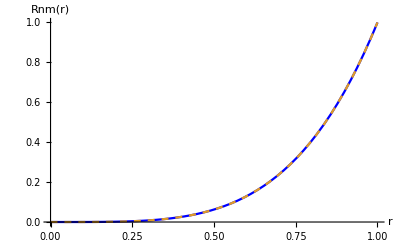

```mathematica
{tn, tm} = {4, 4};
Plot[{R[tn,tm,r], ZernikeR[tn,tm,r]}, {r, 0, 1},PlotStyle->{Blue, Dashed}, AxesLabel->{"r", "Rnm(r)"}]
```

#### Test on the 2D points cloud

Test of orthogonality

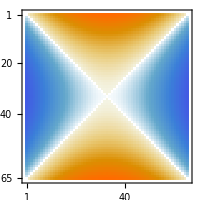

65

```mathematica
test2DOrt= Table[r2c[Z[2,2,r, θ]]//N(*If[Mod[i+j, 2] == 0, 1,0]*), {x,-1, 1, dx}, {y,-1,1, dy}];

MatrixPlot[test2DOrt, ImageSize->200]
Length@test2DOrt
```

```mathematica
Table[{nm⟦1⟧, nm⟦2⟧, A[nm⟦1⟧,nm⟦2⟧,test2DOrt]//N},
{nm, {
{0,0}, 
{1,-1},{1,1}, 
{2,-2}, {2,0}, {2,2},
{3,-3},{3,-1},{3,1},{3,3},
{4,-4},{4,-2},{4,0},{4,2},{4,4}
}}]//TableForm
```

0 | 0 | 0.
1 | -1 | 0.
1 | 1 | 0.
2 | -2 | 0.
2 | 0 | 0.
2 | 2 | 762.246
3 | -3 | 0.
3 | -1 | 0.
3 | 1 | 0.
3 | 3 | 0.
4 | -4 | 0.
4 | -2 | 0.
4 | 0 | 0.
4 | 2 | 406.219
4 | 4 | 0.

```mathematica
(*generators *)
make2DPoint[i_,j_]:=Module[{pointOnPlane},
pointOnPlane = Table[0, {x,-Quotient[maxX,2], Quotient[maxY,2]}, {y,-Quotient[maxX,2], Quotient[maxY,2]}];
pointOnPlane⟦i, j⟧ = -1;

pointOnPlane⟦i, j+2⟧ = -2;
pointOnPlane⟦i, j-2⟧ = -2;
pointOnPlane⟦i+2, j⟧ = -1;
pointOnPlane⟦i-2, j⟧ = -1;
pointOnPlane⟦i-4, j⟧ = -1;

pointOnPlane
]
(* calculate mode indices *)
makeModIndices[n_]:=Table[{n, m}, {m, -n, n, 2}]
(* calcualte descriptor for given size of basis (for given number of harmonics) *)
makeDescriptorTable[IMG_, n_]:=Module[{table},
table = Table[{nm⟦1⟧, nm⟦2⟧, A[nm⟦1⟧,nm⟦2⟧,IMG]//N},
{nm, Flatten[Table[makeModIndices[i],{i, 0, n}],1]}];
table//TableForm
]

makeDescriptorVector[IMG_, n_]:=Module[{table},
table = Table[{nm⟦1⟧, nm⟦2⟧, A[nm⟦1⟧,nm⟦2⟧,IMG]//N},
{nm, Flatten[Table[makeModIndices[i],{i, 0, n}],1]}];
table
]
```

```mathematica
Manipulate[
Row[{MatrixPlot[make2DPoint[y,x], ImageSize->200], makeDescriptorTable[make2DPoint[x,y], 2]}],

{{x, (maxX-1)/2 + 1},1, maxX,1, Appearance->"Open"},
{{y, (maxY-1)/2 + 1},1, maxY,1, Appearance->"Open"}
]
```

```mathematica
coeffs = makeDescriptorVector[make2DPoint[33,33], 10];
recover = Total[#⟦3⟧Table[r2c[Z[#⟦1⟧,#⟦2⟧,r, θ]]//N, {x,-1, 1, dx}, {y,-1,1, dy}]&/@coeffs];
(*
MatrixPlot[recover]*)
```

### 3D Zernike moments

```mathematica
(* definitions of 3D Zernike polynomials *)
(* normalization coefficients *)
```

```mathematica
Q[k_,l_, ν_]:=(-1)^(k+ν)/2^(2k) √((2 l + 4 k + 3)/3)(Binomial[2 k, k] Binomial[k, ν] Binomial[2 (k + l + ν) + 1, 2 k])/Binomial[k +l + ν, k]
R3D[n_, l_, r_]:=Sum[Q[(n-l)/2, l, ν] r^(2 ν + l), {ν, 0, (n-l)/2}]

Z3D[n_, l_,  m_, x_, y_, z_]:=If[x^2+y^2+z^2≤1,(R3D[n, l, r] SphericalHarmonicY[l, m, θ, ϕ])/.{r->√(x^2+y^2+z^2), θ->ArcTan[√(x^2+y^2),z], ϕ->ArcTan[y,x]}, 0]
```

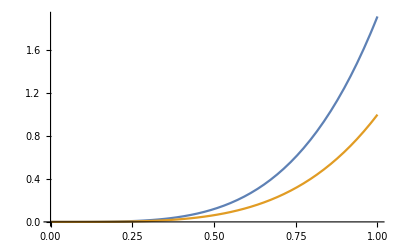

```mathematica
{tn, tl} = {4, 4};
Plot[{R3D[tn, tl, r], R[tn, tl,r]}, {r, 0, 1}]
```

```mathematica
Plot3DZernikeMoment[n_, l_,m_]:=Module[{f, ds, rang, data, dataMcut, plotRow},
f[x_, y_,z_]:=Re[Z3D[n,l,m,x,y,z]];
ds = 0.05;
rang = Join[Range[-1,-ds, ds], Range[ds,1, ds]];
data = Table[f[x, y,z], {x,rang},{y,rang},{z,rang}];
dataMcut = Table[f[x, y,ds], {x,rang},{y,rang}];
plotRow = Row[{
ListDensityPlot3D[data, ColorFunction->"Rainbow", PlotLegends->Automatic, ImageSize->250, PlotRangePadding->None, AxesLabel->{"x", "y", "z"}],
ListDensityPlot[dataMcut, ColorFunction->"Rainbow", ImageSize->250,PlotRangePadding->None]
}];
plotRow
]
```

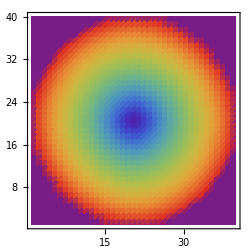
-Graphics3D--Graphics-

```mathematica
Plot3DZernikeMoment[1,1,0]
```

#### Orthogonality check

```mathematica
f1[x_, y_,z_]:=Re[Z3D[1,1,1,x,y,z]];
f2[x_, y_,z_]:=Re[Z3D[4,2,0,x,y,z]];

ds = 0.05;
rang = Join[Range[-1,-ds, ds], Range[ds,1, ds]];
data1 = Table[f1[x, y,z], {x,rang},{y,rang},{z,rang}];
data2 = Table[f2[x, y,z], {x,rang},{y,rang},{z,rang}];

Total[Flatten[data1 data2]]
```

6.59889×10^-15

#### Test on 3D IMG

```mathematica
calcDescr[n_, l_, m_, IMG3D_]:=Module[{f, ds, rang,mode, Z00},
f[x_, y_,z_]:=Re[Z3D[n,l,m,x,y,z]];
ds = 0.05;
rang = Join[Range[-1,-ds, ds], Range[ds,1, ds]];
Z00=  Total@Flatten@Table[Re[Z3D[0,0,0,x,y,z]], {x,rang},{y,rang},{z,rang}];
mode = Table[f[x, y,z], {x,rang},{y,rang},{z,rang}];

Total@Flatten[IMG3D * data / Z00]
]

makeStructure[atomsIonicNum_]:=Module[{ds, rang, grid},
ds = 0.05;
rang = Join[Range[-1,-ds, ds], Range[ds,1, ds]];
grid =Total[ Table[ If[√((x - #⟦1⟧)^2+(y-#⟦2⟧)^2+(z-#⟦3⟧)^2)≤#⟦4⟧, 1, 0], {x,rang},{y,rang},{z,rang}]&/@atomsIonicNum];
grid
]
```

```mathematica
(*testEnv = {{0, 0.75, 0, 0.2}, {0, -0.75, 0, 0.2}, {0.5, 0.4, 0,0.15}, {0.5, -0.4, 0,0.15},{-0.5, 0.4, 0,0.15}, {-0.5, -0.4, 0,0.15},{-0.5, 0, 0.1,0.1},{0.5, 0, 0.1,0.1}};*)
testEnv = {{0, 0.65, 0, 0.2}, {0, -0.65, 0, 0.2}};
test3DIMG = makeStructure[testEnv];
```

```mathematica
ListDensityPlot3D[test3DIMG,  PlotLegends->Automatic, ImageSize->250, PlotRangePadding->None]
```

-Graphics3D-

```mathematica
calcDescr[10,4,2,test3DIMG]
```

-1.87519×10^-19